```mathematica
D[Exp[-β((((x-n)^2)^-α+γ^-α)^(-1/α)+(((x-s)^2)^-α+γ^-α)^(-1/α)+(((x-e)^2)^-α+γ^-α)^(-1/α)+(((x-w)^2)^-α+γ^-α)^(-1/α)+θ(x-y)^2)],x]
```

-ⅇ^(-β ((((-e+x)^2)^-α+γ^-α)^(-1/α)+(((-n+x)^2)^-α+γ^-α)^(-1/α)+(((-s+x)^2)^-α+γ^-α)^(-1/α)+(((-w+x)^2)^-α+γ^-α)^(-1/α)+(x-y)^2 θ)) β (2 (-e+x) ((-e+x)^2)^(-1-α) (((-e+x)^2)^-α+γ^-α)^(-1-1/α)+2 (-n+x) ((-n+x)^2)^(-1-α) (((-n+x)^2)^-α+γ^-α)^(-1-1/α)+2 (-s+x) ((-s+x)^2)^(-1-α) (((-s+x)^2)^-α+γ^-α)^(-1-1/α)+2 (-w+x) ((-w+x)^2)^(-1-α) (((-w+x)^2)^-α+γ^-α)^(-1-1/α)+2 (x-y) θ)

```mathematica
FullSimplify[%]
```

-2 ⅇ^(-β ((((e-x)^2)^-α+γ^-α)^(-1/α)+(((n-x)^2)^-α+γ^-α)^(-1/α)+(((s-x)^2)^-α+γ^-α)^(-1/α)+(((w-x)^2)^-α+γ^-α)^(-1/α)+(x-y)^2 θ)) β ((((e-x)^2)^-α (((e-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-e+x)+(((n-x)^2)^-α (((n-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-n+x)+(((s-x)^2)^-α (((s-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-s+x)+(((w-x)^2)^-α (((w-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-w+x)+(x-y) θ)

$Aborted

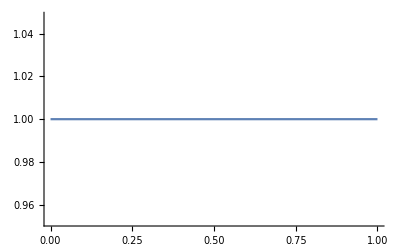

```mathematica
Reduce[%==0 && 0≤x≤1,x]
```

```mathematica
Manipulate[Plot[{Evaluate[D[((((x-n)^2)^-α+γ^-α)^(-1/α)+(((x-s)^2)^-α+γ^-α)^(-1/α)+(((x-e)^2)^-α+γ^-α)^(-1/α)+(((x-w)^2)^-α+γ^-α)^(-1/α))/4+θ(x-y)^2,x]]},{x,0,1},PlotRange->{-.2,.2}],{n,0,1},{s,0,1},{e,0,1},{w,0,1},{y,0,1},{γ,.01,.2},{α,1,2.5},{θ,0,4}]
```

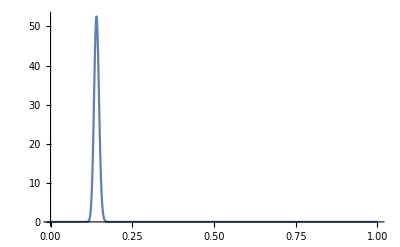

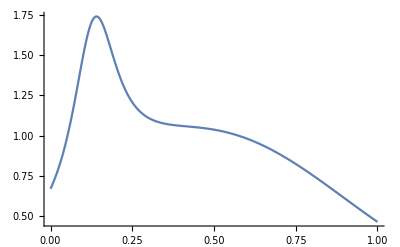

```mathematica
f[x_]:=Exp[-β(((((x-.134)^2)^-α+γ^-α)^(-1/α)+(((x-.144)^2)^-α+γ^-α)^(-1/α)+(((x-.112)^2)^-α+γ^-α)^(-1/α)+(((x-.124)^2)^-α+γ^-α)^(-1/α))/4+θ(x-.5)^2)]/.{γ->.01,α->1,θ->.03,β->10000}
Plot[f[x]/NIntegrate[f[y],{y,0,1}],{x,0,1},PlotRange->All]
```

```mathematica
NIntegrate[f[x],{x,0,1}]
```

0.904022

```mathematica
f[x]
```

ⅇ^(-10 (1/4 (1/(100.+1/(-0.144+x)^2)+1/(100.+1/(-0.134+x)^2)+1/(100.+1/(-0.124+x)^2)+1/(100.+1/(-0.112+x)^2))+0.03 (-0.5+x)^2))